#### Create a sequence of directions

```mathematica
directions =Table[ RandomInteger[3], {50}]
```

{3,2,0,1,3,3,1,2,3,1,3,3,0,2,3,3,0,3,1,2,1,3,0,3,2,1,2,1,1,0,0,3,0,3,3,0,1,0,3,0,0,2,0,0,0,1,2,2,3,3}

#### Create rules that map direction numbers to direction vectors

```mathematica
rules = { 0 -> {0,1}, 1-> {1,0}, 2-> {0,-1} , 3-> {-1,0}}
```

{0→{0,1},1→{1,0},2→{0,-1},3→{-1,0}}

#### Create a table of direction vectors

```mathematica
table =directions/. rules
```

{{0,-1},{0,1},{0,-1},{0,-1},{-1,0},{1,0},{0,1},{1,0},{-1,0},{1,0},{-1,0},{0,-1},{1,0},{0,1},{0,1},{-1,0},{0,1},{-1,0},{0,-1},{0,1},{1,0},{-1,0},{0,-1},{-1,0},{0,-1},{0,1},{-1,0},{-1,0},{1,0},{1,0},{0,-1},{0,1},{-1,0},{0,-1},{0,-1},{-1,0},{1,0},{1,0},{-1,0},{-1,0},{0,-1},{1,0},{0,1},{0,-1},{0,1},{-1,0},{1,0},{1,0},{0,1},{-1,0}}

#### Create sequence of coordinats

```mathematica
coordinates = Accumulate[table]
```

#### Plot the coordinates

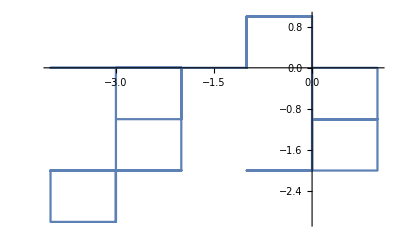

```mathematica
ListLinePlot[coordinates]
```

#### Animate the Plot

```mathematica
Animate[
  ListLinePlot[coordinates[[1;;i]], 
PlotRange->{{-10,10},{-10,10}}, 
AspectRatio->1, GridLines->Automatic],
{i, 1, 50,1}
]
```